Sampling

### Logistic Function

```mathematica
Logistic[x_]:= 1/(1+Exp[-x])
```

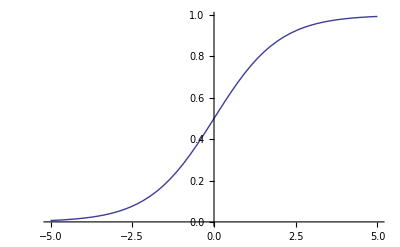

```mathematica
Plot[Logistic[x],{x,-5,5}]
```

### Main Functions

```mathematica
Weight[m_,n_]:=RandomReal[{-1,1},{m,n}]
Visibles[m_]:=RandomInteger[1,m]
Hiddens[n_]:=RandomInteger[1,n]
BiasHiddenSampling[n_]:=RandomInteger[0,n]
BiasVisibleSampling[m_]:=RandomInteger[0,m]
```

### Declarations

```mathematica
SeedRandom[1]
W=Weight[4,5]
V=Visibles[4]
H=Hiddens[5]
BH=BiasHiddenSampling[5]
BV=BiasVisibleSampling[4]
```

{{0.634779,-0.777161,0.579052,-0.624394,-0.517278},{-0.868522,0.0844932,-0.537691,-0.207988,0.400948},{-0.576348,0.497314,-0.154299,-0.50501,0.954344},{0.650326,0.85055,0.156112,-0.414261,-0.583898}}

{1,0,0,1}

{0,1,0,0,1}

{0,0,0,0,0}

{0,0,0,0}

```mathematica
dataV=Table[Visibles[4],{i,10}]
```

{{0,0,1,1},{0,0,1,1},{1,1,1,1},{0,0,1,1},{1,0,0,0},{0,0,1,0},{1,0,1,0},{0,1,0,0},{0,1,0,1},{0,1,1,0}}

```mathematica
V2=Visibles[4]
```

{1,1,1,0}

```mathematica
V3=Visibles[4]
```

{0,1,0,0}

### Sampling Functions

```mathematica
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
sample[l_]:= Sign[Thread[l - RandomReal[1, Length[l]]]];
zsample[l_]:= (Sign[Thread[l - RandomReal[1, Length[l]]]]+1)/2;
SampleHidden[w_][v_]:=sample[Logistic[wᵀ.v]];
SampleVisible[w_][h_]:= sample[Logistic[w.h]];
HiddenProbabilities[w_][v_]:=Logistic[wᵀ.v];
VisibleProbabilities[w_][h_]:= Most[Logistic[w.h]];
```

## Learning

```mathematica
ClearAll[DataLearning,DeltaWeight]
```

```mathematica
DeltaWeight[ϵ_,v1_][w_]:=Module[{h1,v2,h2,w0,w1,wnew,v3,h3},
wnew=w;
Do[
h1=SampleHidden[w][v1];
v2=SampleVisible[w][h1];
h2=SampleHidden[w][v2];
v3=SampleVisible[w][h2];
h3=SampleHidden[w][v3];

(*
w0=1-Outer[BitXor, v1, h1];
w1=1-Outer[BitXor, v1, h3];*)
w0=Outer[Times, v1, h1];
w1=Outer[Times, v1, h3];

wnew += ϵ*(w0-w1);
,
{16}];
wnew
]
```

```mathematica
DataLearning[w_,ϵ_,n_,dataV_]:=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n]
```

```mathematica
StepLearning[w_,ϵ_,n_,dataV_]:=Module[{w1,w2,w3},w1=Nest[Function[DeltaWeight[ϵ,RandomChoice[dataV]][#]],w,n/3];
w2=Nest[Function[DeltaWeight[ϵ/10,RandomChoice[dataV]][#]],w1,n/3];
w3=Nest[Function[DeltaWeight[ϵ/100,RandomChoice[dataV]][#]],w2,n/3];
w3
]
```

```mathematica
square[col_]:=Graphics[Style[Rectangle[],col],ImageSize->10,Frame->True,FrameTicks->False];
numbers2colors[x_]:= x /. {-1 -> square[White], 1->square[Black], r_Real  :> Tooltip[square[Blend[{Red,White,Blue}, r]],r]};
```

## Testing

```mathematica
SeedRandom[5];
Hn=4;Vn=7;
W=RandomReal[{-0.5,0.5},{Vn,Hn}];
dataV=Append[#*2-1,1]& /@ {{1,1,0,1,0,1},{0,0,0,1,1,1},{1,0,1,1,0,0},{0,0,0,1,0,0},{1,1,0,0,1,1}}
w1=StepLearning[W,0.02,4500,dataV];
```

{{1,1,-1,1,-1,1,1},{-1,-1,-1,1,1,1,1},{1,-1,1,1,-1,-1,1},{-1,-1,-1,1,-1,-1,1},{1,1,-1,-1,1,1,1}}

```mathematica
numbers2colors[Most[#]->HiddenProbabilities[w1][#]&/@dataV ]
numbers2colors[#-> VisibleProbabilities[w1][#]&/@Tuples[{-1,1},Hn]]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}→{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}